Valerio Marra (valerio.marra@me.com) -  14/3/2020

## preamble

```mathematica
ClearAll["Global`*"];
$Version
SetDirectory[NotebookDirectory[]];
```

12.0.0 for Mac OS X x86 (64-bit) (April 7, 2019)

## lognormal model for incubation time

```mathematica
PDF[LogNormalDistribution[μ,σ],x]
Mean[LogNormalDistribution[μ,σ]]
Variance[LogNormalDistribution[μ,σ]]
```

Piecewise[{{(ⅇ^(-(-μ+Log[x])^2/(2 σ^2)))/(√(2 π) x σ), x>0}, {0, True}}]

ⅇ^(μ+σ^2/2)

ⅇ^(2 μ+σ^2) (-1+ⅇ^(σ^2))

```mathematica
Solve[{Mean[LogNormalDistribution[μ,σ]]==mu&&Variance[LogNormalDistribution[μ,σ]]==si^2&&mu>0&&si>0&&μ>0&&σ>0},{μ,σ},Reals]
```

{{μ→ConditionalExpression[Log[√(mu^4/(mu^2+si^2))],mu>1&&0<si<√(-mu^2+mu^4)],σ→ConditionalExpression[√2 √Log[mu/(√(mu^4/(mu^2+si^2)))],mu>1&&0<si<√(-mu^2+mu^4)]}}

```mathematica
silogn[mu_,si_]:=√2 √Log[mu/(√(mu^4/(mu^2+si^2)))];
mulogn[mu_,si_]:=Log[√(mu^4/(mu^2+si^2))];
logn[x_,mu_,si_]:=PDF[LogNormalDistribution[mulogn[mu,si],silogn[mu,si]],x];
SetAttributes[logn,Listable];
logns[x_,mu_,si_,b_]:=logn[x-b,mu,si];
```

In the resulting models, estimated median incubation time (IT) of COVID-19 was 5.1 days; mean IT was 5.5 days. For 97.5% of infected persons, symptoms appear by 11.5 days. Fewer than 2.5% are symptomatic within 2.2 days.
https://www.jwatch.org/na51083/2020/03/13/covid-19-incubation-period-update

```mathematica
mu=5.5;
t1=2.2;int1=.025;
t2=11.5;int2=.975;
```

```mathematica
fr=FindRoot[{NIntegrate[logns[x,mu,siv,biv],{x,0,t1},Method->{Automatic,"SymbolicProcessing"->0}],NIntegrate[logns[x,mu,siv,biv],{x,0,t2},Method->{Automatic,"SymbolicProcessing"->0}]}=={int1,int2},{{siv,5},{biv,.5}}]
{si,bi}=fr[[All,2]];
(*NIntegrate[logns[x,mu,si,bi],{x,0,2.2}]
NIntegrate[logns[x,mu,si,bi],{x,0,11.5}]*)
```

{siv→2.4269,biv→-0.00146382}

```mathematica
(* median: good agreement *)
NIntegrate[logns[x,mu,si,bi],{x,0,5.1}]
```

0.512983

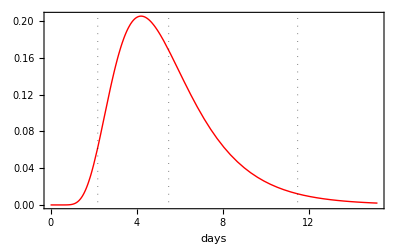

```mathematica
logp=Plot[{logns[x,mu,si,bi]},{x,0,mu+4 si},PlotStyle->{Red,Thick}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,GridLines->{{t1,mu,t2},None},GridLinesStyle->Directive[Black,Thick,Dotted],FrameLabel->{"days"}]
```

```mathematica
Export["logn-incub.png",logp,ImageResolution->300]
```

logn-incub.png

```mathematica
(*NIntegrate[logns[x,mu,si,bi],{x,0,Infinity}]*)
```

## Growth

### positive cases but not necessarily with symptoms

https://www.cnr.it/it/nota-stampa/n-9281/analisi-numerica-dei-dati-relativi-alla-diffusione-del-covid-19-in-italia-e-nel-mondo

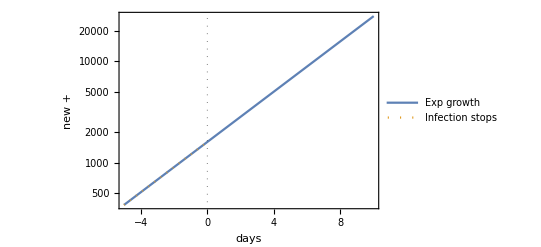

```mathematica
tauv=3.5;
N0v=1600;(*t=0 is March 9*)
tstopv=0; (* the number of new cases stopped on March 9 (guess) *)
cont[t_,tau_,N0_]:=N0 Exp[t/tau];
contStop[t_,tau_,N0_,tStop_]:=If[t<tStop,N0 Exp[t/tau],0];
LogPlot[{cont[t,tauv,N0v],contStop[t,tauv,N0v,tstopv]},{t,-5,10},PlotStyle->{Automatic,Dotted}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,FrameLabel->{"days","new +"},PlotLegends->{"Exp growth","Infection stops"},GridLines->{{tstopv},None},GridLinesStyle->Directive[Black,Thick,Dotted]]
```

```mathematica
contT[t_,tau_,N0_]:=NIntegrate[cont[x,tau,N0],{x,-Infinity,t},Method->{Automatic,"SymbolicProcessing"->0}];
contStopT[t_,tau_,N0_,tStop_]:=NIntegrate[contStop[x,tau,N0,tStop],{x,-Infinity,t},Method->{Automatic,"SymbolicProcessing"->0}];
```

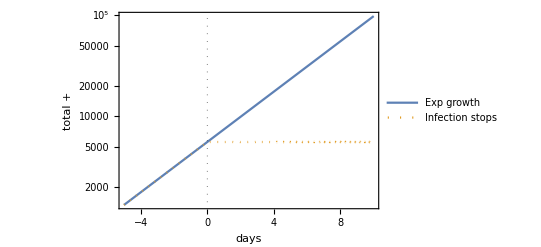

```mathematica
LogPlot[{contT[t,tauv,N0v],contStopT[t,tauv,N0v,tstopv]},{t,-5,10},PlotStyle->{Automatic,Dotted}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,FrameLabel->{"days","total +"},PlotLegends->{"Exp growth","Infection stops"},GridLines->{{tstopv},None},GridLinesStyle->Directive[Black,Thick,Dotted]]
```

### cases with symptoms (delta Dirac)

```mathematica
Integrate[DiracDelta[x-μ],{x,-Infinity,Infinity},Assumptions->μ>0]
Integrate[x DiracDelta[x-μ],{x,-Infinity,Infinity},Assumptions->μ>0]
```

1

μ

```mathematica
Integrate[f[x]DiracDelta[y-x-μ],{x,-Infinity,t},{y,x,t},Assumptions->{μ>0,t>0}]
```

Integrate[f[x] HeavisideTheta[t-x-μ],{x,-∞,t},Assumptions→{μ>0,t>0}]

```mathematica
contDir[t_,tau_,N0_]:=NIntegrate[cont[x,tau,N0]HeavisideTheta[t-x-mu],{x,-Infinity,t},Method->{Automatic,"SymbolicProcessing"->0}];
contStopDir[t_,tau_,N0_,tStop_]:=NIntegrate[contStop[x,tau,N0,tStop]HeavisideTheta[t-x-mu],{x,-Infinity,t},Method->{Automatic,"SymbolicProcessing"->0}];
```

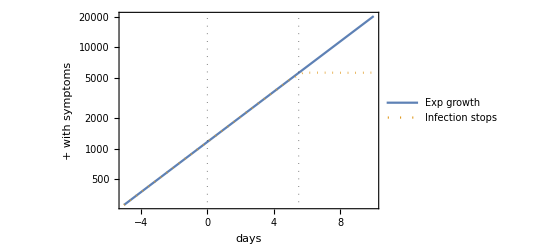

```mathematica
LogPlot[{contDir[t,tauv,N0v],contStopDir[t,tauv,N0v,tstopv]},{t,-5,10},PlotStyle->{Automatic,Dotted}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,FrameLabel->{"days","+ with symptoms"},PlotLegends->{"Exp growth","Infection stops"},GridLines->{{tstopv,mu},None},GridLinesStyle->Directive[Black,Thick,Dotted],PlotPoints->10,MaxRecursion->1]
```

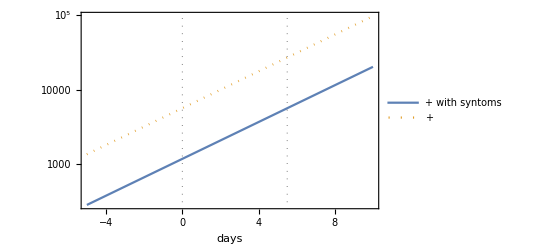

```mathematica
LogPlot[{contDir[t,tauv,N0v],contT[t,tauv,N0v]},{t,-5,10},PlotStyle->{Automatic,Dotted}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,FrameLabel->{"days"},PlotLegends->{"+ with syntoms","+"},GridLines->{{tstopv,mu},None},GridLinesStyle->Directive[Black,Thick,Dotted],PlotPoints->10,MaxRecursion->1]
```

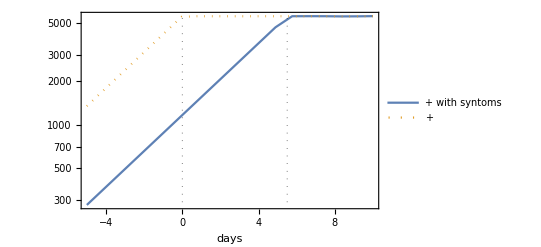

```mathematica
LogPlot[{contStopDir[t,tauv,N0v,tstopv],contStopT[t,tauv,N0v,tstopv]},{t,-5,10},PlotStyle->{Automatic,Dotted}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,FrameLabel->{"days"},PlotLegends->{"+ with syntoms","+"},GridLines->{{tstopv,mu},None},GridLinesStyle->Directive[Black,Thick,Dotted],PlotPoints->10,MaxRecursion->1]
```

### cases with symptoms (lognormal)

```mathematica
contD[t_,tau_,N0_]:=NIntegrate[cont[x,tau,N0]logns[y-x,mu,si,bi],{x,-Infinity,t},{y,x,t},Method->{Automatic,"SymbolicProcessing"->0}];
contStopD[t_,tau_,N0_,tStop_]:=NIntegrate[contStop[x,tau,N0,tStop]logns[y-x,mu,si,bi],{x,-Infinity,t},{y,x,t},Method->{Automatic,"SymbolicProcessing"->0}];
```

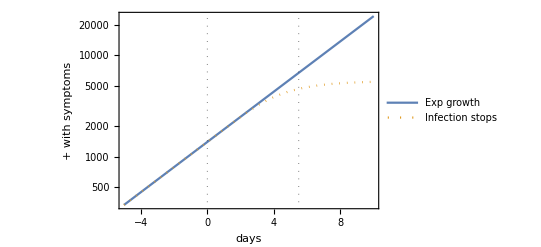

```mathematica
LogPlot[{contD[t,tauv,N0v],contStopD[t,tauv,N0v,tstopv]},{t,-5,10},PlotStyle->{Automatic,Dotted}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,FrameLabel->{"days","+ with symptoms"},PlotLegends->{"Exp growth","Infection stops"},GridLines->{{tstopv,mu},None},GridLinesStyle->Directive[Black,Thick,Dotted],PlotPoints->10,MaxRecursion->1]
```

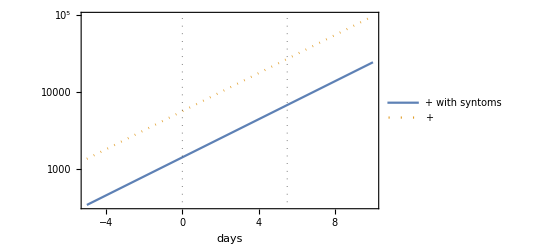

```mathematica
LogPlot[{contD[t,tauv,N0v],contT[t,tauv,N0v]},{t,-5,10},PlotStyle->{Automatic,Dotted}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,FrameLabel->{"days"},PlotLegends->{"+ with syntoms","+"},GridLines->{{tstopv,mu},None},GridLinesStyle->Directive[Black,Thick,Dotted],PlotPoints->10,MaxRecursion->1]
```

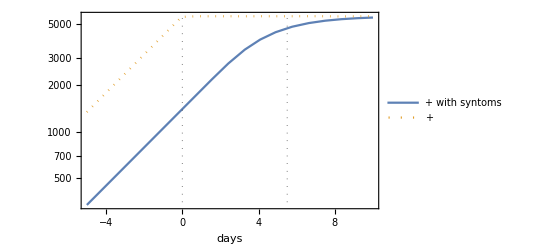

```mathematica
LogPlot[{contStopD[t,tauv,N0v,tstopv],contStopT[t,tauv,N0v,tstopv]},{t,-5,10},PlotStyle->{Automatic,Dotted}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,FrameLabel->{"days"},PlotLegends->{"+ with syntoms","+"},GridLines->{{tstopv,mu},None},GridLinesStyle->Directive[Black,Thick,Dotted],PlotPoints->10,MaxRecursion->1]
```

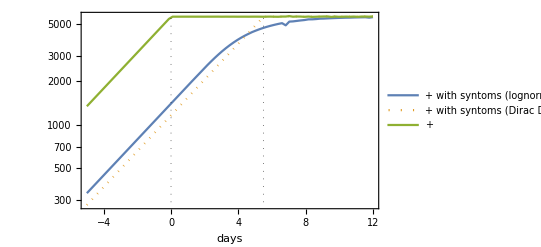

```mathematica
mplot=LogPlot[{contStopD[t,tauv,N0v,tstopv],contStopDir[t,tauv,N0v,tstopv],contStopT[t,tauv,N0v,tstopv]},{t,-5,12},PlotStyle->{Automatic,Dotted}, PlotRange->All,Frame->True,FrameStyle->16,Axes->False,FrameLabel->{"days"},PlotLegends->{"+ with syntoms (lognormal)","+ with syntoms (Dirac Delta)","+"},GridLines->{{tstopv,mu},None},GridLinesStyle->Directive[Black,Thick,Dotted],PlotPoints->20,MaxRecursion->2]
```

```mathematica
Export["logn-curve.png",mplot,ImageResolution->300]
```

logn-curve.png